```mathematica
Clear["Global`*"]
```

```mathematica
(*non*)
data50N=Import["~/BEM/tsukada_floating_body_without_moonpool_a0d75_T5d0_h80/result.json"];
data55N=Import["~/BEM/tsukada_floating_body_without_moonpool_a0d75_T5d5_h80/result.json"];
data60N=Import["~/BEM/tsukada_floating_body_without_moonpool_a0d75_T6d0_h80/result.json"];
data65N=Import["~/BEM/tsukada_floating_body_without_moonpool_a0d75_T6d5_h80/result.json"];
data70N=Import["~/BEM/tsukada_floating_body_without_moonpool_a0d75_T7d0_h80/result.json"];
data75N=Import["~/BEM/tsukada_floating_body_without_moonpool_a0d75_T7d5_h80/result.json"];
data80N=Import["~/BEM/tsukada_floating_body_without_moonpool_a0d75_T8d0_h80/result.json"];
data85N=Import["~/BEM/tsukada_floating_body_without_moonpool_a0d75_T8d5_h80/result.json"];
data90N=Import["~/BEM/tsukada_floating_body_without_moonpool_a0d75_T9d0_h80/result.json"];
data95N=Import["~/BEM/tsukada_floating_body_without_moonpool_a0d75_T9d5_h80/result.json"];
data100N=Import["~/BEM/tsukada_floating_body_without_moonpool_a0d75_T10d0_h80/result.json"];
Do[data75N[[i]][[2]]=data75N[[i]][[2]][[;;547]],{i,1,Length[data75N]}]
```

```mathematica
(*small*)
data50S=Import["~/BEM/moon_pool_small_a0d75_T5d0_h80/result.json"];
data55S=Import["~/BEM/moon_pool_small_a0d75_T5d5_h80/result.json"];
data60S=Import["~/BEM/moon_pool_small_a0d75_T6d0_h80/result.json"];
data65S=Import["~/BEM/moon_pool_small_a0d75_T6d5_h80/result.json"];
data70S=Import["~/BEM/moon_pool_small_a0d75_T7d0_h80/result.json"];
data75S=Import["~/BEM/moon_pool_small_a0d75_T7d5_h80/result.json"];
data80S=Import["~/BEM/moon_pool_small_a0d75_T8d0_h80/result.json"];
data85S=Import["~/BEM/moon_pool_small_a0d75_T8d5_h80/result.json"];
data90S=Import["~/BEM/moon_pool_small_a0d75_T9d0_h80/result.json"];
data95S=Import["~/BEM/moon_pool_small_a0d75_T9d5_h80/result.json"];
data100S=Import["~/BEM/moon_pool_small_a0d75_T10d0_h80/result.json"];
Do[data75S[[i]][[2]]=data75S[[i]][[2]][[;;547]],{i,1,Length[data75S]}]
```

```mathematica
(*large*)
data50=Import["~/BEM/moon_pool_large_a0d75_T5d0_h80/result.json"];
data55=Import["~/BEM/moon_pool_large_a0d75_T5d5_h80/result.json"];
data60=Import["~/BEM/moon_pool_large_a0d75_T6d0_h80/result.json"];
data65=Import["~/BEM/moon_pool_large_a0d75_T6d5_h80/result.json"];
data70=Import["~/BEM/moon_pool_large_a0d75_T7d0_h80/result.json"];
data75=Import["~/BEM/moon_pool_large_a0d75_T7d5_h80/result.json"];
data80=Import["~/BEM/moon_pool_large_a0d75_T8d0_h80/result.json"];
data85=Import["~/BEM/moon_pool_large_a0d75_T8d5_h80/result.json"];
data90=Import["~/BEM/moon_pool_large_a0d75_T9d0_h80/result.json"];
data95=Import["~/BEM/moon_pool_large_a0d75_T9d5_h80/result.json"];
data100=Import["~/BEM/moon_pool_large_a0d75_T10d0_h80/result.json"];

fftPitch[data_]:=Module[{n},n=Length["time"/.data];Return[(2/n)*Abs@Fourier["floatingbody_pitch"/.data]];];
fftHeave[data_]:=Module[{n},n=Length["time"/.data];Return[(2/n)*Abs@Fourier[("floatingbody_COM"/.data)ᵀ[[3]]-75]];];
fftSurge[data_]:=Module[{n},n=Length["time"/.data];Return[(2/n)*Abs@Fourier[("floatingbody_COM"/.data)ᵀ[[1]]-200]];];
getPeriof[data_]:=Module[{n,dt},dt=0.2;n=Length["time"/.data];Return@Table[(i/(n*dt))^-1,{i,1,n,1}]];
getTime[data_]:=Module[{},Return[("time"/.data)];];

fftPitchDEL[data_,del_]:=Module[{n},n=Length["time"/.data];Return[(2/n)*Abs@Fourier[("floatingbody_pitch"/.data)[[;;n-del]]]];];
fftHeaveDEL[data_,del_]:=Module[{n},n=Length[("time"/.data)[[;;n-del]]];Return[(2/n)*Abs@Fourier[("floatingbody_COM"/.data)ᵀ[[3]]-75]];];
fftSurgeDEL[data_,del_]:=Module[{n},n=Length["time"/.data];Return[(2/n)*Abs@Fourier[(("floatingbody_COM"/.data)[[;;n-del]])ᵀ[[1]]-200]];];
getPeriofDEL[data_,del_]:=Module[{n,dt},dt=0.2;n=Length["time"/.data];Return[Table[(i/(n*dt))^-1,{i,1,n,1}][[;;n-del]]]];
getTimeDEL[data_,del_]:=Module[{},Return[("time"/.data)[[;;n-del]]];];
```

```mathematica
Do[data60[[i]][[2]]=data60[[i]][[2]][[;;547]],{i,1,Length[data60]}]
```

```mathematica
opt2D={PlotTheme->"Scientific"
,GridLines->Automatic
,FrameStyle->Directive[Black,FontFamily->"Times New Roman",FontSize->20]};
optC={PlotTheme->"Scientific"
,InterpolationOrder->0
,PlotRangePadding->0
,Contours->1000
,ImageSize->300
,ContourStyle->None
,FrameStyle->Directive[Black,FontFamily->"Times New Roman",FontSize->20]};
opt3D={PlotTheme->"Scientific"
,BoxStyle->Directive[Black,FontFamily->"Times New Roman",FontSize->20]};
```

## Pitch

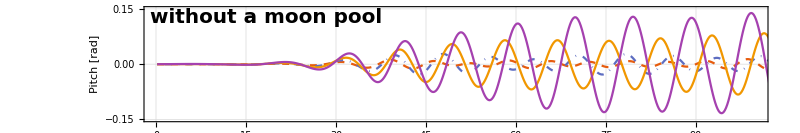
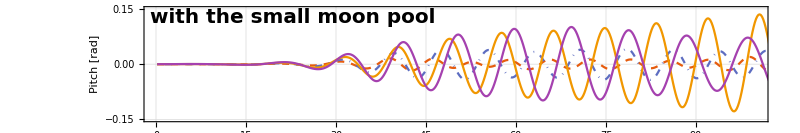
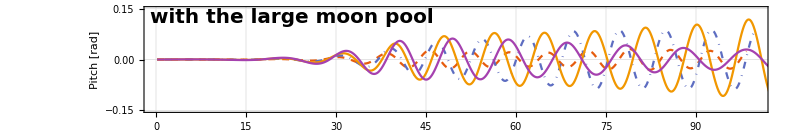

~/Desktop/figNSL_pitch.png

```mathematica
figL=ListPlot[Table[
Transpose[{"time"/.data,"floatingbody_pitch"/.data}]
,{data,{data65,data75,data85, data95}}]
,Joined->True
,FrameTicks->{Automatic,Automatic}
,PlotRange->{{0,100},{-0.15,0.15}}
,PlotStyle->{{Dashed},{DotDashed},{Automatic},{Automatic}}
(*,PlotLegends->{6.5,7.5,8.5, 9.5}*)
,AspectRatio->1/6
,ImageSize->800
,Evaluate[opt2D]
,PlotLegends->{6.5,7.5,8.5, 9.5}
,FrameLabel->{"Time [s]","Pitch [rad]"}
(*,PlotLabel->"with Large moon pool"*)
];

figS=ListPlot[Table[
Transpose[{"time"/.data,"floatingbody_pitch"/.data}]
,{data,{data65S,data75S,data85S, data95S}}]
,Joined->True
,PlotRange->{{0,100},{-0.15,0.15}}
,PlotStyle->{{Dashed},{DotDashed},{Automatic},{Automatic}}
,AspectRatio->1/6
,ImageSize->800
,Evaluate[opt2D]
,FrameLabel->{"","Pitch [rad]"}
];


figN=ListPlot[Table[
Transpose[{"time"/.data,"floatingbody_pitch"/.data}]
,{data,{data65N,data75N,data85N, data95N}}]
,Joined->True
,PlotRange->{{0,100},{-0.15,0.15}}
,PlotStyle->{{Dashed},{DotDashed},{Automatic},{Automatic}}
,AspectRatio->1/6
,ImageSize->800
,Evaluate[opt2D]
,FrameLabel->{"","Pitch [rad]"}
];

Column[{
Legended[figN,Placed[Style["without a moon pool",Black,Bold,20],{Left,Top}]],
Legended[figS,Placed[Style["with the small moon pool",Black,Bold,20],{Left,Top}]],
Legended[figL,Placed[Style["with the large moon pool",Black,Bold,20],{Left,Top}]]
},Spacings->-1.5]
Export["~/塚田/figNSL_pitch.png",%]
```

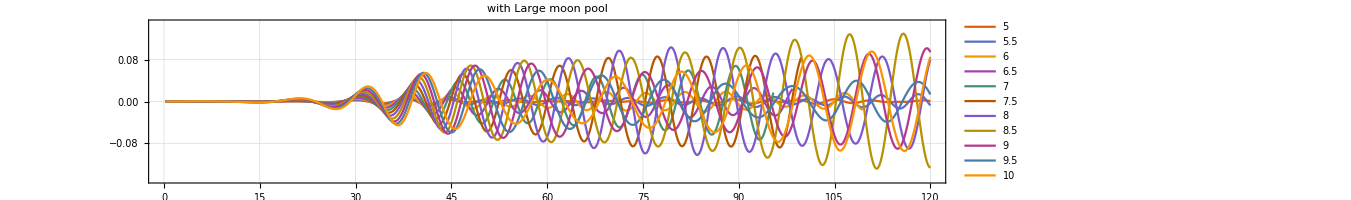

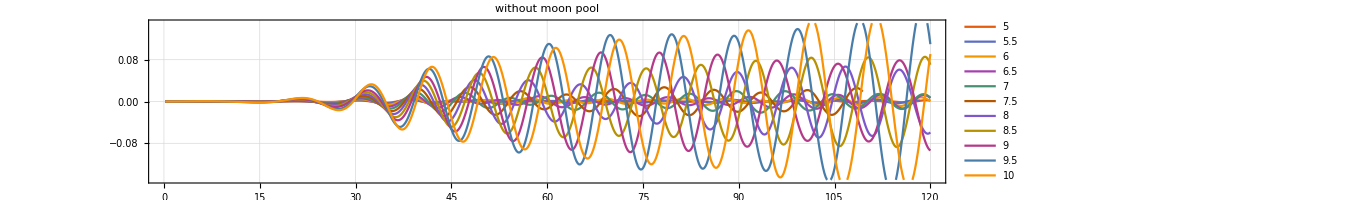

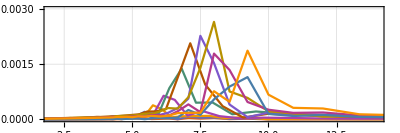

```mathematica
ListPlot[Table[
Transpose[{"time"/.data,"floatingbody_pitch"/.data}]
,{data,{data50,data55,data60,data65,data70,data75,data80,data85,data90, data95, data100}}]
,Joined->True
,PlotRange->{-0.15,0.15}
,PlotLegends->{5,5.5,6,6.5,7,7.5,8,8.5,9, 9.5, 10}
,AspectRatio->1/5
,ImageSize->1000
,Evaluate[opt2D]
,PlotLabel->"with Large moon pool"
]

ListPlot[Table[
Transpose[{"time"/.data,"floatingbody_pitch"/.data}]
,{data,{data50N,data55N,data60N,data65N,data70N,data75N,data80N,data85N,data90N, data95N, data100N}}]
,Joined->True
,PlotRange->{-0.15,0.15}
,PlotLegends->{5,5.5,6,6.5,7,7.5,8,8.5,9, 9.5, 10}
,AspectRatio->1/5
,ImageSize->1000
,Evaluate[opt2D]
,PlotLabel->"without moon pool"
]

ListPlot[Table[
Transpose[{getPeriof[data],fftPitch[data]}]
,{data,{data50,data55,data60,data65,data70,data75,data80,data85,data90, data95, data100}}]
,Joined->True
,PlotRange->{{2,14},{0,3*10^-3}}
,PlotLegends->{5,5.5,6,6.5,7,7.5,8,8.5,9, 9.5, 10}
,AspectRatio->1/3
,Evaluate[opt2D]
]


tabL=Flatten[Table[
Transpose[{
getPeriof[data[[2]]],
Table[data[[1]],{i,1,Length[getPeriof[data[[2]]]]}],
fftPitch[data[[2]]]}]
,{data,{{5,data50},{5.5,data55},{6,data60},{6.5,data65},{7.,data70},{7.5,data75},{8.,data80},{8.5,data85},{9.,data90},{9.5,data95},{10.,data100}}}],1];

tabS=Flatten[Table[
Transpose[{
getPeriof[data[[2]]],
Table[data[[1]],{i,1,Length[getPeriof[data[[2]]]]}],
fftPitch[data[[2]]]}]
,{data,{{5,data50S},{5.5,data55S},{6,data60S},{6.5,data65S},{7.,data70S},{7.5,data75S},{8.,data80S},{8.5,data85S},{9.,data90S},{9.5,data95S},{10.,data100S}}}],1];


tabN=Flatten[Table[
Transpose[{
getPeriof[dataN[[2]]],
Table[dataN[[1]],{i,1,Length[getPeriof[dataN[[2]]]]}],
fftPitch[dataN[[2]]]}]
,{dataN,{{5,data50N},{5.5,data50N},{6,data60N},{6.5,data65N},{7.,data70N},{7.5,data75N},{8.,data80N},{8.5,data85N},{9.,data90N},{9.5,data95N},{10.,data100N}}}],1];

(*ListPlot3D[Flatten[tab,1]
,PlotRange->{{0,0.3},Automatic,All}

,Mesh->All
,BoxRatios->{1,1,0.5}
,Filling->Axis
,AxesLabel->{"Period [s]","Incident [m]","FFT"}
,ImageSize->700
,ColorFunction->"SouthwestColors"
,Evaluate[opt3D]]*)
```

{0.,0.004}

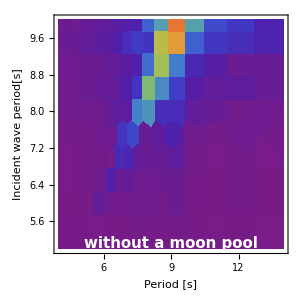
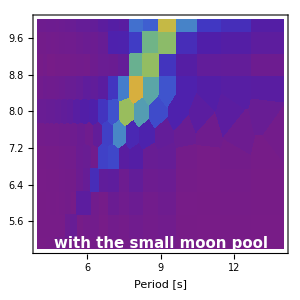
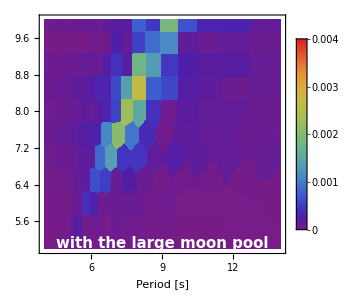
-Graphics- | -Graphics- | -Graphics-

~/Desktop/contourNSL_pitch.png

```mathematica
{min,max}={0.,0.004}
contourL=ListContourPlot[tabL
,ColorFunctionScaling->False
,ColorFunction->(ColorData["Rainbow"][Rescale[#,{min,max}]]&)
,PlotRange->{{4,14},Automatic,{0,0.004}}
,FrameLabel->{"Period [s]",""}
,Evaluate[optC]
,PlotLegends->BarLegend[{ColorData["Rainbow"][Rescale[#,{min,max}]]&,{min,max}}]
];

contourS=ListContourPlot[tabS
,ColorFunctionScaling->False
,ColorFunction->(ColorData["Rainbow"][Rescale[#,{min,max}]]&)
,PlotRange->{{4,14},Automatic,{0,0.004}}
,FrameLabel->{"Period [s]",""}
,Evaluate[optC]
(*,PlotLegends->BarLegend[{ColorData["Rainbow"][Rescale[#,{min,max}]]&,{min,max}}]*)
];

contourN=ListContourPlot[tabN
,ColorFunctionScaling->False
,ColorFunction->(ColorData["Rainbow"][Rescale[#,{min,max}]]&)
,PlotRange->{{4,14},Automatic,{0,0.004}}
,FrameLabel->{"Period [s]","Incident wave period[s]"}
,Evaluate[optC]
(*,PlotLegends->BarLegend[{ColorData["Rainbow"][Rescale[#,{min,max}]]&,{min,max}}]*)
];

Grid[{{
Legended[contourN,Placed[Style["without a moon pool",White,Bold,15],{Center,Bottom}]],
Legended[contourS,Placed[Style["with the small moon pool",White,Bold,15],{Center,Bottom}]],
Legended[contourL,Placed[Style["with the large moon pool",White,Bold,15],{Center,Bottom}]]
}},Spacings->-0.6]
Export["~/Desktop/contourNSL_pitch.png",%]
```

## Pitch

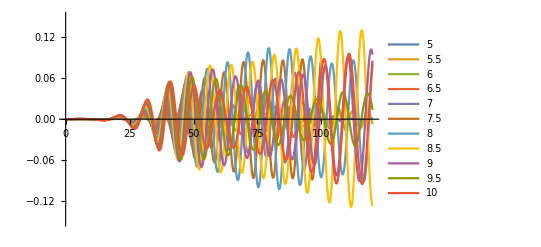

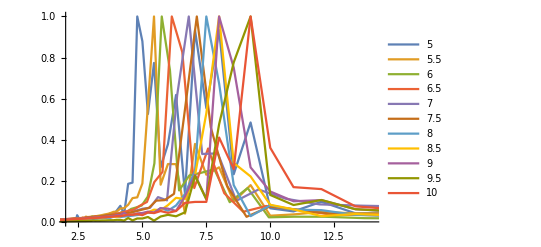

-Graphics3D-

```mathematica
ListPlot[Table[
Transpose[{"time"/.data,"floatingbody_pitch"/.data}]
,{data,{data50,data55,data60,data65,data70,data75,data80,data85,data90, data95, data100}}]
,Joined->True
,PlotRange->{-0.15,0.15}
,PlotLegends->{5,5.5,6,6.5,7,7.5,8,8.5,9, 9.5, 10}
]

ListPlot[Table[
{#1,#2/Max[fftPitch[data]]}&@@@Transpose[{getPeriof[data],fftPitch[data]}]
,{data,{data50,data55,data60,data65,data70,data75,data80,data85,data90, data95, data100}}]
,Joined->True
,PlotRange->{{2,14},{0,1}}
,PlotLegends->{5,5.5,6,6.5,7,7.5,8,8.5,9, 9.5, 10}
]

ListPlot3D[Flatten[
Table[
{#1,#2,#3/Max[fftPitch[data[[2]]]]}&@@@Transpose[{
getPeriof[data[[2]]],
Table[data[[1]],{i,1,Length[getPeriof[data[[2]]]]}],
fftPitch[data[[2]]]}]
,{data,{{5,data50},{5.5,data55},{6,data60},{6.5,data65},{7.,data70},{7.5,data75},{8.,data80},{8.5,data85},{9.,data90},{9.5,data95},{10.,data100}}}],1],
PlotRange->{{2,14},{5,10},{0,1}},
AxesLabel->{"Period [s]","Incident [m]","FFT"},
TicksStyle->Black,
AxesStyle->Directive[{Black,FontSize->15,FontFamily->"Times"}],
ImageSize->400,
ColorFunction->"SouthwestColors"
]
```

## Surge

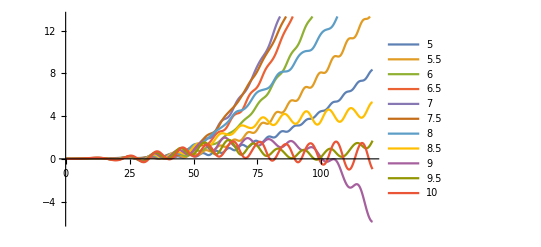

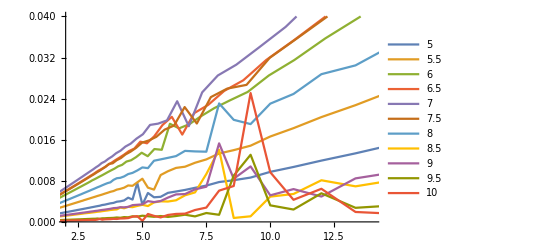

```mathematica
ListPlot[Table[
Transpose[{getTime[data],("floatingbody_COM"/.data)ᵀ[[1]]-200}]
,{data,{data50,data55,data60,data65,data70,data75,data80,data85,data90, data95, data100}}]
,Joined->True
,PlotLegends->{5,5.5,6,6.5,7,7.5,8,8.5,9, 9.5, 10}
]

ListPlot[Table[
Transpose[{getPeriof[data],fftSurge[data]}]
,{data,{data50,data55,data60,data65,data70,data75,data80,data85,data90, data95, data100}}]
,Joined->True
,PlotRange->{{2,14},{0,4*10^-2}}
,PlotLegends->{5,5.5,6,6.5,7,7.5,8,8.5,9, 9.5, 10}
]
```

## Heave

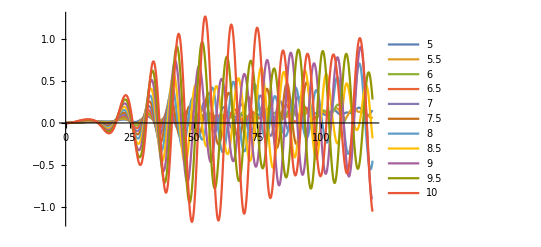

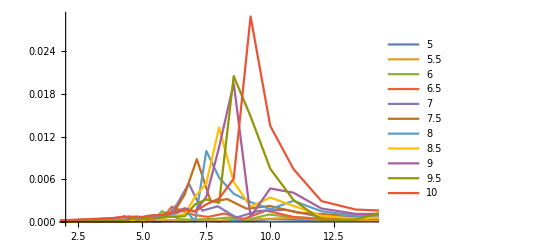

-Graphics3D-

```mathematica
ListPlot[Table[
Transpose[{getTime[data],("floatingbody_COM"/.data)ᵀ[[3]]-75}]
,{data,{data50,data55,data60,data65,data70,data75,data80,data85,data90, data95, data100}}]
,Joined->True
,PlotRange->All
,PlotLegends->{5,5.5,6,6.5,7,7.5,8,8.5,9, 9.5, 10}
]

ListPlot[Table[
Transpose[{getPeriof[data],fftHeave[data]}]
,{data,{data50,data55,data60,data65,data70,data75,data80,data85,data90, data95, data100}}]
,Joined->True
,PlotRange->{{2,14},All}
,PlotLegends->{5,5.5,6,6.5,7,7.5,8,8.5,9, 9.5, 10}
]

ListPlot3D[Flatten[
Table[
Transpose[{
getPeriof[data[[2]]],
Table[data[[1]],{i,1,Length[getPeriof[data[[2]]]]}],
fftHeave[data[[2]]]}]
,{data,{{5,data50},{5.5,data55},{6,data60},{6.5,data65},{7.,data70},{7.5,data75},{8.,data80},{8.5,data85},{9.,data90},{9.5,data95},{10.,data100}}}],1],
PlotRange->{{2,14},{5,10},All},
AxesLabel->{"Period [s]","Incident [m]","FFT"},
TicksStyle->Black,
AxesStyle->Directive[{Black,FontSize->15,FontFamily->"Times"}],
ImageSize->400,
ColorFunction->"SouthwestColors"
]
```

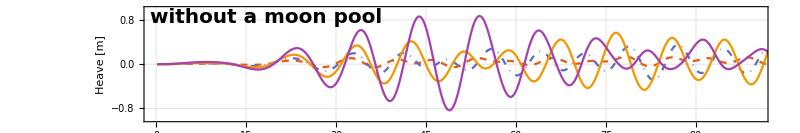
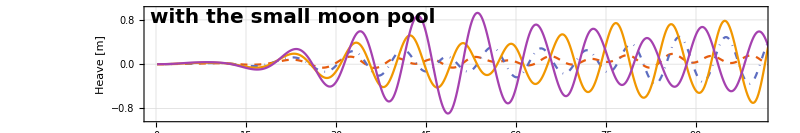
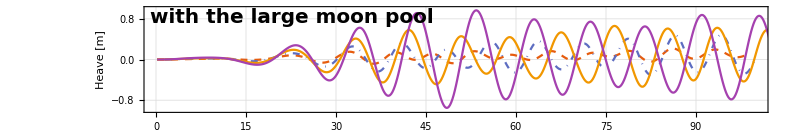

~/Desktop/figNSL_heave.png

```mathematica
figL=ListPlot[Table[
Transpose[{getTime[data],("floatingbody_COM"/.data)ᵀ[[3]]-75}]
,{data,{data65,data75,data85, data95}}]
,Joined->True
,FrameTicks->{Automatic,Automatic}
,PlotRange->{{0,100},{-1.,1.}}
,PlotStyle->{{Dashed},{DotDashed},{Automatic},{Automatic}}
(*,PlotLegends->{6.5,7.5,8.5, 9.5}*)
,AspectRatio->1/6
,ImageSize->800
,Evaluate[opt2D]
,FrameLabel->{"Time [s]","Heave [m]"}
,PlotLegends->{6.5,7.5,8.5, 9.5}
(*,PlotLabel->"with Large moon pool"*)
];


figS=ListPlot[Table[
Transpose[{getTime[data],("floatingbody_COM"/.data)ᵀ[[3]]-75}]
,{data,{data65S,data75S,data85S, data95S}}]
,Joined->True
,FrameTicks->{Automatic,Automatic}
,PlotRange->{{0,100},{-1.,1.}}
,PlotStyle->{{Dashed},{DotDashed},{Automatic},{Automatic}}
(*,PlotLegends->{6.5,7.5,8.5, 9.5}*)
,AspectRatio->1/6
,ImageSize->800
,Evaluate[opt2D]
,FrameLabel->{"","Heave [m]"}
(*,PlotLegends->{6.5,7.5,8.5, 9.5}*)
(*,PlotLabel->"with Large moon pool"*)
];

figN=ListPlot[Table[
Transpose[{getTime[data],("floatingbody_COM"/.data)ᵀ[[3]]-75}]
,{data,{data65N,data75N,data85N, data95N}}]
,Joined->True
,PlotRange->{{0,100},{-1.,1.}}
,PlotStyle->{{Dashed},{DotDashed},{Automatic},{Automatic}}
,AspectRatio->1/6
,ImageSize->800
,Evaluate[opt2D]
,FrameLabel->{"","Heave [m]"}
];
Column[{
Legended[figN,Placed[Style["without a moon pool",Black,Bold,20],{Left,Top}]],
Legended[figS,Placed[Style["with the small moon pool",Black,Bold,20],{Left,Top}]],
Legended[figL,Placed[Style["with the large moon pool",Black,Bold,20],{Left,Top}]]
},Spacings->-1]
Export["~/Desktop/figNSL_heave.png",%]
```

```mathematica
tabL=Flatten[Table[
Transpose[{
getPeriof[data[[2]]],
Table[data[[1]],{i,1,Length[getPeriof[data[[2]]]]}],
fftHeave[data[[2]]]}]
,{data,{{5,data50},{5.5,data55},{6,data60},{6.5,data65},{7.,data70},{7.5,data75},{8.,data80},{8.5,data85},{9.,data90},{9.5,data95},{10.,data100}}}],1];

tabS=Flatten[Table[
Transpose[{
getPeriof[data[[2]]],
Table[data[[1]],{i,1,Length[getPeriof[data[[2]]]]}],
fftHeave[data[[2]]]}]
,{data,{{5,data50S},{5.5,data55S},{6,data60S},{6.5,data65S},{7.,data70S},{7.5,data75S},{8.,data80S},{8.5,data85S},{9.,data90S},{9.5,data95S},{10.,data100S}}}],1];

tabN=Flatten[Table[
Transpose[{
getPeriof[dataN[[2]]],
Table[dataN[[1]],{i,1,Length[getPeriof[dataN[[2]]]]}],
fftHeave[dataN[[2]]]}]
,{dataN,{{5,data50N},{5.5,data50N},{6,data60N},{6.5,data65N},{7.,data70N},{7.5,data75N},{8.,data80N},{8.5,data85N},{9.,data90N},{9.5,data95N},{10.,data100N}}}],1];


{min,max}={0.,0.04}
contourL=ListContourPlot[tabL
,ColorFunctionScaling->False
,ColorFunction->(ColorData["Rainbow"][Rescale[#,{min,max}]]&)
,PlotRange->{{4,14},Automatic,{min,max}}
,FrameLabel->{"Period [s]",""}
,Evaluate[optC]
,PlotLegends->BarLegend[{ColorData["Rainbow"][Rescale[#,{min,max}]]&,{min,max}}]
,Background->Opacity[0]
];

contourS=ListContourPlot[tabS
,ColorFunctionScaling->False
,ColorFunction->(ColorData["Rainbow"][Rescale[#,{min,max}]]&)
,PlotRange->{{4,14},Automatic,{min,max}}
,FrameLabel->{"Period [s]",""}
,Evaluate[optC]
(*,PlotLegends->BarLegend[{ColorData["Rainbow"][Rescale[#,{min,max}]]&,{min,max}}]*)
,Background->Opacity[0]
];


contourN=ListContourPlot[tabN
,ColorFunctionScaling->False
,ColorFunction->(ColorData["Rainbow"][Rescale[#,{min,max}]]&)
,PlotRange->{{4,14},Automatic,{min,max}}
,Evaluate[optC]
,FrameLabel->{"Period [s]","Incident wave period[s]"}
(*,PlotLegends->BarLegend[{ColorData["Rainbow"][Rescale[#,{min,max}]]&,{min,max}}]*)
,Background->Opacity[0]
];
```

{0.,0.04}

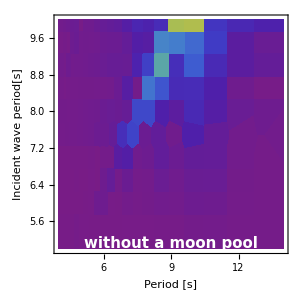
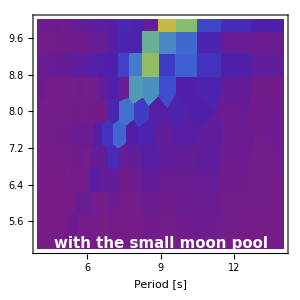
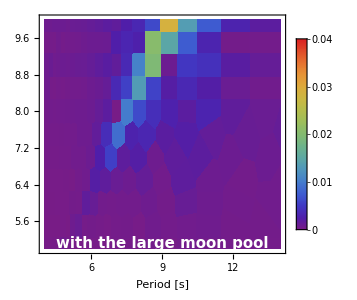
-Graphics- | -Graphics- | -Graphics-

~/Desktop/contourNSL_heave.png

```mathematica
Grid[{{
Legended[contourN,Placed[Style["without a moon pool",White,Bold,15],{Center,Bottom}]],
Legended[contourS,Placed[Style["with the small moon pool",White,Bold,15],{Center,Bottom}]],
Legended[contourL,Placed[Style["with the large moon pool",White,Bold,15],{Center,Bottom}]]
}},Spacings->-.6,Background->None]
Export["~/Desktop/contourNSL_heave.png",%]
```